```mathematica
Nt = 551 ;(*151*)
ti = 0; tf =1; 
deltat = (tf - ti) /Nt ;
Nx = 551; (*151*)
(*xi = -2; xf = 8; *)
(*xi = 0; xf = 2*Pi;*)
xi = 0; xf = 2*Pi;
deltax = (xf - xi) / Nx;
c = 1;
r = c * (deltat / deltax)//N
k = .;
j  = .;
```

0.159155

```mathematica
(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)
h = N[(2*Pi)/ (Nx),32];

T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];
Xo = N[Table[xn = xi + n *deltax, {n, 0, Nx -1}],32];

X = N[(Xo-xi)*((2*Pi))/(xf-xi),32];

f[x_] = ⅇ^(- 8(x-π)^2);
```

```mathematica
(************************************************************************************************************************)
(*Differentiation Matrix*)
(************************************************************************************************************************)
```

```mathematica
D1 = N[Table[If[ k≠ j, 1/2(-1)^(k - j)Csc[((k - j) * h)/2],0],{k,1,Nx},{j,1,Nx}],32];
D2 = N[MatrixPower[D1,2],32];
DL = N[-c * D1 * deltat,32];
```

```mathematica
(*CN*)
UCN= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCN[[1,All]] = N[f[X],32];
UCN = N[UCN,32];
UCN = Chop[UCN, 10^(-307)];
UCN = Developer`ToPackedArray[UCN, Real]; 
Developer`PackedArrayQ[UCN]

UCNold= N[Table[0, {n, 1, Nt}, {m, 1, Nx }],32];
UCNold[[1,All]] = N[f[X],32];
UCNold = N[UCNold,32];
UCNold = Chop[UCNold, 10^(-307)];
UCNold = Developer`ToPackedArray[UCNold, Real]; 
Developer`PackedArrayQ[UCNold]


I1 = N[IdentityMatrix[Length[D1]],32];
A = N[I1 - ((DL / 2)),32];
B = N[I1 + ((DL / 2)),32];
MCN = N[Inverse[A].B,32];
EMCN = N[MCN - I1,32];
EMCN = Developer`ToPackedArray[EMCN, Real]; 

Do[UCNold[[n+1,All]] = UCNold[[n,All]] + (EMCN).UCNold[[n,All]], {n,1,Nt - 1 }];
Do[
Do[
UCN[[n+1,m]] = UCN[[n,m]] +  Total[EMCN[[m,All]] * UCN[[n,All]]]

,{m,1,Length[EMCN]}]
,{n,1,Nt - 1}]
```

True

True

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*Energy*)
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
(*CN*)
FCN = Table[0,{i,1,Nt},{j,1,Nx}];
FCN = Developer`ToPackedArray[FCN, Real];
intCN = Table[0,{i,1,Length[FCN[[All,1]]]}];
intCN = Developer`ToPackedArray[intCN, Real];

FCNold = Table[0,{i,1,Nt},{j,1,Nx}];
FCNold = Developer`ToPackedArray[FCNold, Real];
intCNold = Table[0,{i,1,Length[FCNold[[All,1]]]}];
intCNold = Developer`ToPackedArray[intCNold, Real];
Do[
FCN[[i]] = (D1.UCN[[i,All]])^2;

intCN[[i]] = (2π)/Nx Total[FCN[[i,All]]]
,{i,1,Length[FCN[[All,1]]]}];

Do[
FCNold[[i]] = (D1.UCNold[[i,All]])^2;

intCNold[[i]] = (2π)/Nx Total[FCNold[[i,All]]]
,{i,1,Length[FCNold[[All,1]]]}];
```

```mathematica
energyErrorLD2 = Abs[intCN - intCN[[1]]];
energyErrorLD2old = Abs[intCNold - intCNold[[1]]];
energyErrorLD2 - energyErrorLD2old
```

{0.,4.88498×10^-15,7.10543×10^-15,-5.77316×10^-15,-3.55271×10^-15,-8.88178×10^-15,3.9968×10^-15,1.15463×10^-14,1.33227×10^-15,-8.88178×10^-16,-8.88178×10^-15,-3.10862×10^-15,-9.76996×10^-15,6.21725×10^-15,0.,6.66134×10^-15,2.66454×10^-15,-1.28786×10^-14,8.88178×10^-16,5.77316×10^-15,5.77316×10^-15,2.66454×10^-15,-4.44089×10^-16,-1.11022×10^-14,3.9968×10^-15,2.22045×10^-15,-8.88178×10^-15,6.21725×10^-15,1.55431×10^-14,-3.10862×10^-15,3.55271×10^-15,-5.77316×10^-15,0.,-7.54952×10^-15,-4.44089×10^-15,1.11022×10^-14,-4.44089×10^-15,6.21725×10^-15,-7.54952×10^-15,-3.55271×10^-15,5.32907×10^-15,-8.88178×10^-16,-8.88178×10^-16,7.99361×10^-15,-3.9968×10^-15,-3.10862×10^-15,-5.77316×10^-15,8.43769×10^-15,-8.88178×10^-16,3.9968×10^-15,-4.88498×10^-15,-8.88178×10^-15,-4.88498×10^-15,8.88178×10^-16,-1.77636×10^-15,8.88178×10^-16,-4.88498×10^-15,3.55271×10^-15,7.10543×10^-15,-1.33227×10^-15,-2.35367×10^-14,1.5099×10^-14,1.33227×10^-15,1.06581×10^-14,-7.10543×10^-15,6.21725×10^-15,3.10862×10^-15,3.9968×10^-15,1.33227×10^-15,5.32907×10^-15,1.19904×10^-14,1.06581×10^-14,1.86517×10^-14,6.66134×10^-15,0.,3.55271×10^-15,-3.55271×10^-15,5.77316×10^-15,4.44089×10^-15,-1.19904×10^-14,8.88178×10^-16,-5.77316×10^-15,4.88498×10^-15,3.9968×10^-15,7.10543×10^-15,1.11022×10^-14,-1.33227×10^-15,5.77316×10^-15,-1.68754×10^-14,-1.33227×10^-15,3.55271×10^-15,-1.77636×10^-15,-6.21725×10^-15,6.66134×10^-15,7.99361×10^-15,6.66134×10^-15,-1.19904×10^-14,2.66454×10^-15,4.44089×10^-16,5.32907×10^-15,-7.99361×10^-15,-9.76996×10^-15,-8.43769×10^-15,4.44089×10^-16,-2.22045×10^-15,6.66134×10^-15,8.88178×10^-16,-5.32907×10^-15,-2.66454×10^-15,2.22045×10^-15,-8.88178×10^-16,-1.77636×10^-14,-3.55271×10^-15,-3.10862×10^-15,3.55271×10^-15,1.15463×10^-14,-2.66454×10^-15,-7.10543×10^-15,-1.06581×10^-14,3.10862×10^-15,-1.15463×10^-14,1.33227×10^-15,-4.44089×10^-16,-4.88498×10^-15,2.66454×10^-15,-3.10862×10^-15,-5.32907×10^-15,3.55271×10^-15,5.32907×10^-15,9.76996×10^-15,-2.66454×10^-15,9.76996×10^-15,4.88498×10^-15,3.55271×10^-15,7.10543×10^-15,-2.66454×10^-15,8.88178×10^-15,1.77636×10^-15,-3.55271×10^-15,2.22045×10^-15,-5.32907×10^-15,-1.33227×10^-15,4.44089×10^-16,1.24345×10^-14,9.76996×10^-15,3.55271×10^-15,-1.64313×10^-14,9.32587×10^-15,1.77636×10^-14,6.21725×10^-15,-9.32587×10^-15,-7.10543×10^-15,1.24345×10^-14,6.21725×10^-15,1.06581×10^-14,0.,-8.43769×10^-15,8.43769×10^-15,-7.54952×10^-15,-2.44249×10^-14,5.32907×10^-15,6.21725×10^-15,-2.22045×10^-15,2.08722×10^-14,4.44089×10^-16,1.24345×10^-14,-1.5099×10^-14,1.77636×10^-14,-6.21725×10^-15,7.99361×10^-15,7.99361×10^-15,7.54952×10^-15,-4.88498×10^-15,-2.66454×10^-15,-3.9968×10^-15,0.,3.10862×10^-15,1.06581×10^-14,-2.22045×10^-15,-2.66454×10^-15,3.10862×10^-15,-5.77316×10^-15,-3.9968×10^-15,2.66454×10^-15,-4.88498×10^-15,-4.44089×10^-15,1.82077×10^-14,-7.54952×10^-15,3.9968×10^-15,6.21725×10^-15,0.,-8.43769×10^-15,-3.55271×10^-15,3.9968×10^-15,6.21725×10^-15,6.21725×10^-15,1.64313×10^-14,-4.44089×10^-16,-4.88498×10^-15,3.9968×10^-15,1.11022×10^-14,3.55271×10^-15,0.,-1.37668×10^-14,9.76996×10^-15,8.88178×10^-16,7.10543×10^-15,3.9968×10^-15,-1.11022×10^-14,3.55271×10^-15,5.77316×10^-15,-6.66134×10^-15,-1.77636×10^-15,-6.21725×10^-15,3.55271×10^-15,-4.44089×10^-16,2.22045×10^-15,3.55271×10^-15,0.,1.82077×10^-14,8.43769×10^-15,-7.10543×10^-15,1.68754×10^-14,5.77316×10^-15,4.88498×10^-15,7.10543×10^-15,-4.88498×10^-15,8.88178×10^-15,-3.10862×10^-15,7.10543×10^-15,7.99361×10^-15,5.32907×10^-15,4.88498×10^-15,3.55271×10^-15,7.99361×10^-15,-4.88498×10^-15,1.33227×10^-15,-1.19904×10^-14,8.43769×10^-15,3.55271×10^-15,-6.21725×10^-15,-5.77316×10^-15,-4.88498×10^-15,8.88178×10^-16,-1.11022×10^-14,-4.44089×10^-15,6.66134×10^-15,1.68754×10^-14,7.10543×10^-15,1.33227×10^-15,-1.77636×10^-15,-1.33227×10^-15,8.88178×10^-15,3.55271×10^-15,0.,8.43769×10^-15,1.37668×10^-14,-4.44089×10^-16,1.19904×10^-14,-7.10543×10^-15,8.88178×10^-15,5.77316×10^-15,-4.88498×10^-15,-8.43769×10^-15,-6.66134×10^-15,-1.19904×10^-14,3.9968×10^-15,0.,-1.19904×10^-14,-7.54952×10^-15,-1.02141×10^-14,1.33227×10^-15,-7.99361×10^-15,-8.43769×10^-15,3.55271×10^-15,7.10543×10^-15,2.66454×10^-15,4.88498×10^-15,-2.66454×10^-15,-8.43769×10^-15,-1.9984×10^-14,1.28786×10^-14,1.33227×10^-14,1.46549×10^-14,9.76996×10^-15,1.33227×10^-15,-4.88498×10^-15,1.19904×10^-14,-3.9968×10^-15,-8.88178×10^-16,-1.33227×10^-15,-1.02141×10^-14,9.76996×10^-15,4.44089×10^-15,1.24345×10^-14,-1.82077×10^-14,-3.55271×10^-15,8.43769×10^-15,6.21725×10^-15,-3.9968×10^-15,-7.99361×10^-15,1.11022×10^-14,3.55271×10^-15,-5.77316×10^-15,3.10862×10^-15,1.82077×10^-14,-6.66134×10^-15,1.55431×10^-14,4.88498×10^-15,1.33227×10^-15,1.15463×10^-14,-6.21725×10^-15,-7.99361×10^-15,1.06581×10^-14,-2.66454×10^-15,-4.44089×10^-16,4.88498×10^-15,1.06581×10^-14,1.55431×10^-14,0.,1.15463×10^-14,1.55431×10^-14,-8.88178×10^-15,9.76996×10^-15,-1.24345×10^-14,-1.33227×10^-15,8.88178×10^-15,1.11022×10^-14,-4.44089×10^-15,-1.33227×10^-14,-6.21725×10^-15,1.33227×10^-15,1.24345×10^-14,0.,-2.66454×10^-15,1.33227×10^-14,7.54952×10^-15,-1.59872×10^-14,-2.22045×10^-15,1.64313×10^-14,-2.22045×10^-15,1.33227×10^-15,7.99361×10^-15,-5.77316×10^-15,-6.21725×10^-15,5.77316×10^-15,1.95399×10^-14,3.28626×10^-14,-4.88498×10^-15,-1.11022×10^-14,-1.46549×10^-14,0.,3.55271×10^-15,1.15463×10^-14,8.88178×10^-16,9.76996×10^-15,-4.88498×10^-15,6.21725×10^-15,7.10543×10^-15,-6.66134×10^-15,1.24345×10^-14,-3.55271×10^-15,8.43769×10^-15,5.32907×10^-15,4.88498×10^-15,-1.24345×10^-14,1.02141×10^-14,3.55271×10^-15,-6.21725×10^-15,-1.33227×10^-15,2.44249×10^-14,-4.88498×10^-15,-3.55271×10^-15,9.32587×10^-15,-4.44089×10^-16,3.55271×10^-15,2.57572×10^-14,-5.77316×10^-15,-1.28786×10^-14,-6.66134×10^-15,-6.66134×10^-15,-6.21725×10^-15,-5.77316×10^-15,2.57572×10^-14,1.37668×10^-14,7.10543×10^-15,-4.44089×10^-16,5.77316×10^-15,-4.88498×10^-15,6.21725×10^-15,5.77316×10^-15,1.86517×10^-14,1.19904×10^-14,-8.88178×10^-16,-9.76996×10^-15,1.68754×10^-14,1.19904×10^-14,-2.22045×10^-15,3.55271×10^-15,5.77316×10^-15,1.42109×10^-14,1.33227×10^-14,8.43769×10^-15,2.22045×10^-14,0.,-9.32587×10^-15,5.77316×10^-15,9.76996×10^-15,4.44089×10^-16,1.77636×10^-15,0.,-1.06581×10^-14,5.77316×10^-15,8.43769×10^-15,-5.77316×10^-15,0.,1.02141×10^-14,1.9984×10^-14,4.44089×10^-16,-3.55271×10^-15,1.19904×10^-14,2.13163×10^-14,-3.9968×10^-15,-2.66454×10^-15,3.9968×10^-15,-1.02141×10^-14,6.21725×10^-15,8.88178×10^-15,0.,-1.06581×10^-14,-8.43769×10^-15,-8.88178×10^-16,-1.33227×10^-14,7.99361×10^-15,1.06581×10^-14,-2.22045×10^-15,4.44089×10^-16,1.68754×10^-14,2.22045×10^-15,1.37668×10^-14,2.22045×10^-15,-9.76996×10^-15,-1.11022×10^-14,6.21725×10^-15,4.88498×10^-15,1.11022×10^-14,-2.66454×10^-15,7.99361×10^-15,-9.32587×10^-15,1.37668×10^-14,6.66134×10^-15,-1.33227×10^-15,-2.22045×10^-15,2.08722×10^-14,3.10862×10^-15,3.55271×10^-15,0.,-4.88498×10^-15,1.11022×10^-14,-5.77316×10^-15,-4.44089×10^-15,1.9984×10^-14,2.35367×10^-14,-1.55431×10^-14,1.59872×10^-14,3.9968×10^-15,7.54952×10^-15,3.55271×10^-15,1.37668×10^-14,-6.66134×10^-15,1.46549×10^-14,4.88498×10^-15,1.33227×10^-15,-3.55271×10^-15,-4.88498×10^-15,7.10543×10^-15,0.,-4.44089×10^-16,1.02141×10^-14,1.46549×10^-14,5.32907×10^-15,5.77316×10^-15,8.88178×10^-15,3.9968×10^-15,3.9968×10^-15,-4.88498×10^-15,-1.33227×10^-14,1.82077×10^-14,1.95399×10^-14,6.66134×10^-15,4.44089×10^-15,6.21725×10^-15,0.,1.19904×10^-14,-6.21725×10^-15,2.66454×10^-15,4.88498×10^-15,1.55431×10^-14,-2.66454×10^-15,1.11022×10^-14,2.30926×10^-14,1.28786×10^-14,1.28786×10^-14,8.88178×10^-16,1.15463×10^-14,0.,7.54952×10^-15,8.88178×10^-16,1.68754×10^-14,-1.77636×10^-14,-5.77316×10^-15,1.11022×10^-14,1.42109×10^-14,8.88178×10^-15,-3.10862×10^-15,-7.54952×10^-15,6.21725×10^-15,2.17604×10^-14,1.15463×10^-14,6.66134×10^-15,4.44089×10^-16,1.73195×10^-14,1.73195×10^-14,-8.43769×10^-15,-2.66454×10^-15,0.,0.,-5.32907×10^-15,1.11022×10^-14,-7.10543×10^-15,2.30926×10^-14,3.10862×10^-15,4.13003×10^-14,-7.54952×10^-15,-1.33227×10^-14,-1.33227×10^-15,-8.43769×10^-15,2.66454×10^-15,8.43769×10^-15,1.68754×10^-14,5.32907×10^-15,7.54952×10^-15,1.19904×10^-14,1.95399×10^-14,1.11022×10^-14,9.32587×10^-15,1.06581×10^-14,6.66134×10^-15,3.55271×10^-15,9.76996×10^-15,1.24345×10^-14}

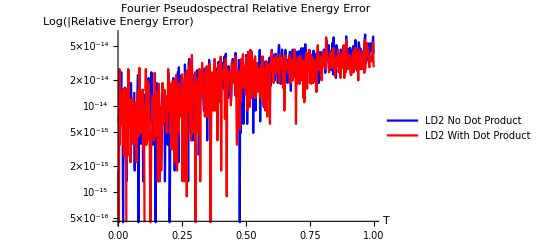

```mathematica
ListLogPlot[{Transpose[{T,energyErrorLD2}],Transpose[{T,energyErrorLD2old}]},PlotStyle->{Blue,Red},PlotLegends->{"LD2 No Dot Product", "LD2 With Dot Product"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Fourier Pseudospectral Relative Energy Error",PlotRange->{{ti,tf},{0,Max[energyErrorLD2]}},Joined->True]
```

```mathematica
(*exportData=Flatten/@Transpose[{T,energyErrorLD2, energyErrorLD4, energyErrorRK2, energyErrorRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\Energy_Error_Pseudospectral.dat",exportData,"Table"];*)
```

```mathematica
(*exportDataRK4Stable=Flatten/@Transpose[{T,intRK4}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\FDM_RK4_Stable_Energy.dat",exportDataRK4Stable,"Table"];*)
```

```mathematica
(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)
```

```mathematica
fexact[t_,x_] = ⅇ^(- 8((x-t)-π)^2);
Uexact = Table[fexact[T[[i]],X[[j]]],{i,1,Nt},{j,1,Nx}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Real];
```

```mathematica
(*LD2*)
abserrLD2 = Abs[UCN-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];
(*ListLinePlot[Transpose[{T,errorLD2}],PlotRange->All]*)

abserrLD2old = Abs[UCNold-Uexact];
errorLD2old = Table[0,{i,1,Length[abserrLD2old]}];
errorLD2old = Developer`ToPackedArray[errorLD2old, Real];
Do[
errorLD2old[[i]] = Norm[abserrLD2old[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2old]}
];

errorLD2 - errorLD2old
```

{0.,-1.38407×10^-17,-3.75372×10^-18,1.53104×10^-18,3.12881×10^-18,4.78595×10^-18,-3.4344×10^-18,8.49148×10^-18,2.30923×10^-17,1.87051×10^-17,5.51032×10^-18,4.24374×10^-18,7.96899×10^-18,1.00058×10^-17,5.03836×10^-18,-2.26835×10^-18,-1.65451×10^-17,-1.57449×10^-17,-2.28562×10^-17,-1.07593×10^-17,-9.73971×10^-18,8.18943×10^-18,-2.98029×10^-18,-1.14434×10^-17,3.56368×10^-18,1.61803×10^-17,2.64045×10^-17,3.79017×10^-17,3.82604×10^-17,4.46916×10^-18,1.4685×10^-17,1.60212×10^-17,2.25359×10^-17,2.76624×10^-17,3.50934×10^-17,1.45906×10^-17,2.4345×10^-17,3.94417×10^-17,3.129×10^-17,2.70642×10^-17,2.19079×10^-17,1.23053×10^-17,-8.49362×10^-19,-8.53809×10^-18,2.90299×10^-18,1.22398×10^-17,1.25031×10^-17,3.75043×10^-17,-1.1857×10^-17,-7.69762×10^-18,-1.81763×10^-17,-1.1865×10^-17,-1.43185×10^-17,7.50408×10^-18,-7.09665×10^-18,-1.8261×10^-17,-5.99932×10^-18,-4.15237×10^-18,9.65745×10^-18,1.62385×10^-17,-1.36499×10^-18,7.29211×10^-18,1.17384×10^-17,5.15801×10^-18,4.59431×10^-18,9.34913×10^-18,-6.44931×10^-18,-2.42912×10^-17,-2.21978×10^-17,-3.16257×10^-17,-2.55406×10^-17,-1.9029×10^-17,2.14003×10^-18,-2.2548×10^-17,-2.41443×10^-17,-3.52442×10^-17,-1.77657×10^-17,-1.55791×10^-17,-2.14299×10^-17,-3.98292×10^-17,-4.19709×10^-17,-3.42422×10^-17,-5.5418×10^-17,-5.3823×10^-17,-4.39246×10^-17,-7.66599×10^-17,-7.45872×10^-17,-6.46379×10^-17,-6.37697×10^-17,-5.52613×10^-17,-3.46445×10^-17,-1.24099×10^-17,-4.51486×10^-17,-3.67714×10^-17,-4.86307×10^-17,-3.83935×10^-17,-2.31752×10^-17,-1.25191×10^-17,-3.14194×10^-17,-2.62195×10^-17,-2.89673×10^-17,-2.51166×10^-17,-1.22981×10^-17,-7.91976×10^-18,-1.80977×10^-17,-2.66032×10^-17,-3.29284×10^-17,-3.57181×10^-17,-2.6394×10^-17,-5.80938×10^-18,-2.51018×10^-18,-1.41526×10^-17,-1.87728×10^-17,-4.72522×10^-17,-4.56923×10^-17,-3.48347×10^-17,-2.63952×10^-17,-5.41767×10^-17,-6.19338×10^-17,-6.11299×10^-17,-5.63069×10^-17,-6.09915×10^-17,-5.34914×10^-17,-6.10266×10^-17,-5.54104×10^-17,-5.57195×10^-17,-7.07641×10^-17,-6.46532×10^-17,-6.86292×10^-17,-6.64972×10^-17,-6.93288×10^-17,-5.96642×10^-17,-5.9848×10^-17,-7.11821×10^-17,-7.11923×10^-17,-3.7383×10^-17,-7.32014×10^-17,-8.54885×10^-17,-8.96932×10^-17,-9.5713×10^-17,-9.85006×10^-17,-7.71283×10^-17,-6.54748×10^-17,-7.45262×10^-17,-7.47896×10^-17,-8.33675×10^-17,-6.54231×10^-17,-7.38553×10^-17,-3.54619×10^-17,-4.26422×10^-17,-6.50699×10^-17,-7.87004×10^-17,-7.9799×10^-17,-7.73553×10^-17,-2.57396×10^-17,-5.9327×10^-17,-7.23349×10^-17,-8.40316×10^-17,-1.04758×10^-16,-9.66219×10^-17,-9.36259×10^-17,-5.04137×10^-17,-6.86757×10^-17,-9.91782×10^-17,-1.23167×10^-16,-1.35469×10^-16,-1.44827×10^-16,-9.46204×10^-17,-1.07215×10^-16,-1.2968×10^-16,-1.53484×10^-16,-1.77458×10^-16,-1.89931×10^-16,-1.39018×10^-16,-1.45331×10^-16,-1.47452×10^-16,-1.57229×10^-16,-1.58287×10^-16,-1.68076×10^-16,-1.31736×10^-16,-1.33697×10^-16,-1.45621×10^-16,-1.48707×10^-16,-1.64878×10^-16,-1.75109×10^-16,-1.86372×10^-16,-1.24366×10^-16,-1.35287×10^-16,-1.39873×10^-16,-1.5065×10^-16,-1.51597×10^-16,-1.69683×10^-16,-1.2688×10^-16,-1.32511×10^-16,-1.3188×10^-16,-1.38108×10^-16,-1.4843×10^-16,-1.69762×10^-16,-1.13196×10^-16,-1.55775×10^-16,-1.56698×10^-16,-1.51456×10^-16,-1.64418×10^-16,-1.70274×10^-16,-1.9881×10^-16,-1.57928×10^-16,-1.64166×10^-16,-1.58574×10^-16,-1.60774×10^-16,-1.61436×10^-16,-1.80349×10^-16,-1.38208×10^-16,-1.64199×10^-16,-1.72396×10^-16,-1.65705×10^-16,-1.55796×10^-16,-1.52017×10^-16,-9.8011×10^-17,-1.27971×10^-16,-1.28487×10^-16,-1.30472×10^-16,-1.36933×10^-16,-1.42988×10^-16,-1.24883×10^-16,-1.55428×10^-16,-1.83795×10^-16,-1.76179×10^-16,-1.61048×10^-16,-1.67357×10^-16,-1.9043×10^-16,-1.55046×10^-16,-1.92546×10^-16,-2.16843×10^-16,-2.13341×10^-16,-1.93426×10^-16,-1.85847×10^-16,-1.21003×10^-16,-1.77212×10^-16,-1.95339×10^-16,-2.18911×10^-16,-1.90305×10^-16,-1.70116×10^-16,-6.10397×10^-17,-1.42155×10^-16,-1.92489×10^-16,-2.12198×10^-16,-2.08279×10^-16,-1.83718×10^-16,-1.69668×10^-16,-1.17119×10^-16,-1.86227×10^-16,-2.34809×10^-16,-2.50407×10^-16,-2.29048×10^-16,-1.90135×10^-16,-1.10074×10^-16,-1.78119×10^-16,-2.15355×10^-16,-2.51974×10^-16,-2.44574×10^-16,-2.10274×10^-16,-9.27027×10^-17,-1.29931×10^-16,-1.82878×10^-16,-2.39866×10^-16,-2.66084×10^-16,-2.22566×10^-16,-1.28712×10^-16,-8.54165×10^-17,-1.47609×10^-16,-2.15851×10^-16,-2.53763×10^-16,-2.44867×10^-16,-2.11987×10^-16,-8.39003×10^-17,-1.37572×10^-16,-1.95912×10^-16,-2.52309×10^-16,-2.8443×10^-16,-2.43264×10^-16,-1.02179×10^-16,-9.44526×10^-17,-1.37479×10^-16,-2.01653×10^-16,-2.5434×10^-16,-2.4731×10^-16,-8.15862×10^-17,-8.25095×10^-17,-1.22381×10^-16,-1.77403×10^-16,-2.42651×10^-16,-2.61743×10^-16,-2.24282×10^-16,-7.5496×10^-17,-6.80371×10^-17,-1.04039×10^-16,-1.84614×10^-16,-2.51022×10^-16,-2.38865×10^-16,-9.10018×10^-17,-6.99581×10^-17,-1.08734×10^-16,-1.83288×10^-16,-2.6483×10^-16,-2.97697×10^-16,-1.69444×10^-16,-1.23494×10^-16,-1.12523×10^-16,-1.53406×10^-16,-2.43183×10^-16,-2.88591×10^-16,-2.26197×10^-16,-1.2749×10^-16,-9.94468×10^-17,-1.32357×10^-16,-2.01506×10^-16,-2.82943×10^-16,-3.13124×10^-16,-1.74831×10^-16,-1.14671×10^-16,-1.20396×10^-16,-1.83039×10^-16,-2.75279×10^-16,-3.38457×10^-16,-2.17135×10^-16,-1.62637×10^-16,-1.15125×10^-16,-1.46886×10^-16,-2.10833×10^-16,-2.92259×10^-16,-2.03535×10^-16,-1.89044×10^-16,-1.34656×10^-16,-1.3374×10^-16,-1.66796×10^-16,-2.56583×10^-16,-2.68503×10^-16,-1.90521×10^-16,-1.37411×10^-16,-1.02233×10^-16,-1.18742×10^-16,-1.99458×10^-16,-2.869×10^-16,-2.12539×10^-16,-1.91826×10^-16,-1.43015×10^-16,-1.18076×10^-16,-1.58995×10^-16,-2.59233×10^-16,-2.10122×10^-16,-2.25258×10^-16,-1.99674×10^-16,-1.6592×10^-16,-1.74065×10^-16,-2.44389×10^-16,-2.84086×10^-16,-2.62316×10^-16,-2.54344×10^-16,-2.12078×10^-16,-1.82459×10^-16,-2.07755×10^-16,-2.90104×10^-16,-2.22795×10^-16,-2.52933×10^-16,-2.15919×10^-16,-1.88775×10^-16,-1.91733×10^-16,-2.4009×10^-16,-1.7993×10^-16,-2.48482×10^-16,-2.56138×10^-16,-2.16181×10^-16,-1.96183×10^-16,-2.27381×10^-16,-1.66362×10^-16,-2.43856×10^-16,-2.87507×10^-16,-2.66893×10^-16,-2.22116×10^-16,-2.08592×10^-16,-2.16657×10^-16,-1.9271×10^-16,-2.75257×10^-16,-2.87312×10^-16,-2.44332×10^-16,-2.14252×10^-16,-2.30899×10^-16,-1.36486×10^-16,-2.31169×10^-16,-2.75748×10^-16,-2.45929×10^-16,-1.93208×10^-16,-1.69327×10^-16,-8.01344×10^-17,-1.64396×10^-16,-2.41924×10^-16,-2.50366×10^-16,-2.02661×10^-16,-1.66184×10^-16,-1.82857×10^-17,-1.02352×10^-16,-2.1188×10^-16,-2.51137×10^-16,-2.30036×10^-16,-1.75722×10^-16,-1.66706×10^-16,-6.21807×10^-17,-1.64448×10^-16,-2.44249×10^-16,-2.55706×10^-16,-2.13805×10^-16,-1.60233×10^-16,-7.70292×10^-18,-9.73207×10^-17,-2.19104×10^-16,-2.68481×10^-16,-2.32861×10^-16,-1.72325×10^-16,1.92327×10^-17,-4.86773×10^-17,-1.80142×10^-16,-2.63232×10^-16,-2.72628×10^-16,-2.03559×10^-16,-1.08693×10^-16,-1.14316×10^-17,-1.16794×10^-16,-2.393×10^-16,-2.8699×10^-16,-2.49234×10^-16,-1.69593×10^-16,7.50471×10^-18,-5.66885×10^-17,-2.03908×10^-16,-2.97021×10^-16,-3.02459×10^-16,-2.24301×10^-16,-9.49185×10^-18,-8.06206×10^-18,-1.27445×10^-16,-2.5298×10^-16,-2.99123×10^-16,-2.47862×10^-16,-9.77984×10^-18,2.48909×10^-17,-5.33139×10^-17,-1.95327×10^-16,-2.82777×10^-16,-2.74368×10^-16,-1.93117×10^-16,1.83959×10^-17,-1.64799×10^-17,-1.6228×10^-16,-2.78721×10^-16,-3.179×10^-16,-2.5708×10^-16,-4.05678×10^-17,-1.69356×10^-17,-1.28022×10^-16,-2.76319×10^-16,-3.61598×10^-16,-3.26277×10^-16,-8.64312×10^-17,-9.89334×10^-18,-5.71391×10^-17,-2.1064×10^-16,-3.27609×10^-16,-3.65485×10^-16,-2.49509×10^-16,-3.00968×10^-17,-6.37646×10^-18,-1.34311×10^-16,-2.90636×10^-16,-3.77396×10^-16,-3.38607×10^-16,-6.37341×10^-17,-5.84961×10^-18,-7.62279×10^-17,-2.47974×10^-16,-3.83809×10^-16,-3.97592×10^-16,-1.56274×10^-16,-4.94701×10^-17,-5.24754×10^-17,-1.75532×10^-16,-3.28061×10^-16,-4.04268×10^-16,-2.3435×10^-16,-1.22024×10^-16,-6.11236×10^-17,-1.3819×10^-16,-2.83795×10^-16,-4.06596×10^-16,-4.22629×10^-16,-1.77406×10^-16,-8.18725×10^-17,-9.8061×10^-17,-2.27061×10^-16,-3.61026×10^-16,-4.13618×10^-16,-2.198×10^-16,-1.02455×10^-16,-6.84199×10^-17,-1.58212×10^-16,-3.24505×10^-16,-4.25912×10^-16,-2.9038×10^-16,-1.8139×10^-16,-8.98024×10^-17,-1.29762×10^-16,-2.70424×10^-16,-4.06694×10^-16,-4.39305×10^-16,-2.4178×10^-16,-1.2508×10^-16,-1.01305×10^-16,-2.25267×10^-16,-3.79115×10^-16,-4.74515×10^-16,-3.17143×10^-16,-1.96884×10^-16,-1.37829×10^-16,-1.92707×10^-16,-3.41974×10^-16,-4.69544×10^-16,-3.79674×10^-16,-2.86094×10^-16,-1.68702×10^-16,-1.63145×10^-16,-2.81544×10^-16,-4.45329×10^-16,-3.93138×10^-16,-3.47883×10^-16,-2.08631×10^-16,-1.53608×10^-16,-2.255×10^-16,-3.8519×10^-16,-5.06729×10^-16,-3.82351×10^-16,-2.74117×10^-16,-1.65981×10^-16,-1.84629×10^-16,-3.15909×10^-16,-4.60474×10^-16,-4.11007×10^-16,-3.47714×10^-16,-2.23163×10^-16,-1.92642×10^-16,-2.71542×10^-16,-4.34084×10^-16,-4.41087×10^-16}

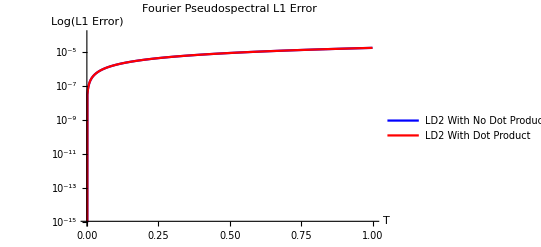

```mathematica
ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorLD2old}]},PlotRange->{{ti,tf},{1*10^-15,1*10^-4}}, PlotStyle->{Blue, Red},PlotLegends->{"LD2 With No Dot Product", "LD2 With Dot Product"},Axes -> True, AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"Fourier Pseudospectral L1 Error", Joined->True]
```